This notebook uses MaTeX to generate LaTeX-style labels for graphics. If you haven’t already installed MaTeX but you’re using Mathematica version 11.3 or later, just execute the command

	ResourceFunction[“MaTeXInstall”][]

to complete installation. If you’re using an older version of Mathematica, you can find installation instructions at http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html.

```mathematica
<<MaTeX`
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

```mathematica
matex18 := MaTeX[#, FontSize->18]&
```

In this notebook we model a variation of the three-link swimmer in an ideal fluid. The three links are ellipses separated by gaps. The forward hinge (joining the “body” to the “head”) is actuated while the rear hinge (joining the “body” to the “tail”) is spring-loaded. Let’s begin by specifying physical parameters and options and drawing a manipulable picture of the swimmer.

```mathematica
dotRadius = 1/2;
gapBT = 3/2;
gapBH = 3/2;
ρ = 1;
area = 18 π;
bT = area / (π aT);
bB = area / (π aB);
bH = area / (π aH);
equalGaps = {gapTB -> gapBT, gapHB -> gapBH};
equalLeverage = {gapTB -> aB + gapBT - aT, gapHB -> aB + gapBH - aH};
bodyCenter = {x[t], y[t]};
headPivot = bodyCenter + {(aB + gapBH) Cos[θ[t]], (aB + gapBH) Sin[θ[t]]};
headCenter = headPivot + {(gapHB + aH) Cos[θ[t] + η[t]],(gapHB + aH) Sin[θ[t] + η[t]]};
tailPivot = bodyCenter - {(aB + gapBT) Cos[θ[t]], (aB + gapBT) Sin[θ[t]]};
tailCenter = tailPivot - {((gapTB + aT)) Cos[θ[t] - τ[t]],(gapTB + aT) Sin[θ[t] - τ[t]]};
body = Graphics[{LightPink, EdgeForm[Black],Disk[bodyCenter, {aB, bB}]  // Rotate[#, θ[t], bodyCenter]& }];
headPivotDot = Disk[headPivot, dotRadius] // Graphics;
head = Graphics[{LightPink, EdgeForm[Black],Disk[headCenter, {aH, bH}]  // Rotate[#, θ[t] + η[t], headCenter]& }];
tailPivotDot = Disk[tailPivot, dotRadius] // Graphics;
tail = Graphics[{LightPink, EdgeForm[Black],Disk[tailCenter, {aT, bT}]  // Rotate[#, θ[t] - τ[t], tailCenter]& }];
water = Graphics[{LightBlue, Rectangle[{-500, -500}, {500, 500}]}];
robotLength = 2 aT + gapTB + gapBT + 2 aB + gapBH + gapHB + 2 aH;
```

```mathematica
cartoon[aTail_, aBody_, aHead_]:=Manipulate[Show[{water, body, headPivotDot, head, tailPivotDot, tail} /. equalGaps /.  {aT -> aTail, aB -> aBody, aH -> aHead} /.{x[t] -> X, y[t] -> Y, θ[t] -> Θ, η[t] -> Η, τ[t] -> Τ}, PlotRange -> {{-robotLength, robotLength}, {-robotLength, robotLength}}  /. equalGaps  /. {aT -> aTail, aB -> aBody, aH -> aHead}], {{X, 0}, -5, 5}, {{Y, 0}, -5 ,5} , {{Θ, 0}, - π, π}, {{Η, 0}, -π/2, π/2}, {{Τ, 0}, -π/2, π/2}]
```

You can vary the three arguments to the cartoon command below to realize swimmers with different link geometries. The three arguments represent the semimajor axes of the three ellipses, from tail to head.

```mathematica
cartoon[7, 7, 7]
```

Now let’s model the system’s dynamics.

```mathematica
bodyHeading = {Cos[θ[t]], Sin[θ[t]]};
bodyHeadingPerp = {- Sin[θ[t]], Cos[θ[t]]};
headHeading = {Cos[θ[t] + η[t]], Sin[θ[t] + η[t]]};
headHeadingPerp = {- Sin[θ[t] + η[t]], Cos[θ[t] + η[t]]};
tailHeading = {Cos[θ[t] - τ[t]], Sin[θ[t] - τ[t]]};
tailHeadingPerp = {-Sin[θ[t] - τ[t]], Cos[θ[t] - τ[t]]};
bodyVelocity = D[bodyCenter, t];
bodyKE = 1/2 mLongB (bodyVelocity.bodyHeading)^2 + 1/2 mLatB (bodyVelocity.bodyHeadingPerp)^2 + 1/2 mRotB (θ'[t])^2;
headVelocity = D[headCenter, t];
headKE = 1/2 mLongH (headVelocity.headHeading)^2 + 1/2 mLatH(headVelocity.headHeadingPerp)^2 + 1/2 mRotH (θ'[t] + η'[t])^2;
tailVelocity = D[tailCenter, t];
tailKE = 1/2 mLongT (tailVelocity.tailHeading)^2 + 1/2 mLatT (tailVelocity.tailHeadingPerp)^2+ 1/2 mRotT (θ'[t] - τ'[t])^2;
tailPE = 1/2 k τ[t]^2;
```

The Lagrangian for the system is

```mathematica
L = bodyKE + headKE + tailKE - tailPE;
```

We're interested in the behavior of the system on the zero level set of linear and angular momentum. This behavior is governed by the mechanical connection obtained as follows.

First, let's verify that the Lagrangian is invariant under left translation in SE(2). Here’s the lifted action on the tangent bundle of the configuration manifold:

```mathematica
liftedAction = {x[t] -> xbar + x[t] Cos[θbar] - y[t] Sin[θbar], y[t] -> ybar + x[t] Sin[θbar] + y[t] Cos[θbar],
θ[t] -> θ[t] + θbar, x'[t] -> x'[t] Cos[θbar] - y'[t] Sin[θbar], 
y'[t] -> x'[t] Sin[θbar] + y'[t] Cos[θbar]};
```

Do these substitutions alter the Lagrangian?

```mathematica
Simplify[L - (L /. liftedAction)]
```

0

Nope. So there’s an SE(2) symmetry. If we order the coordinates on Q as (x, y, θ, η, τ), then the infinitesimal generators associated with two arbitrary Lie algebra elements can be written thus:

```mathematica
ζ = {ζ1, ζ2, ζ3};
```

```mathematica
ζQ = {ζ1 - y[t] ζ3, ζ2 + x[t] ζ3, ζ3, 0, 0};
```

```mathematica
λ = {λ1, λ2, λ3};
```

```mathematica
λQ = {λ1 - y[t] λ3, λ2 + x[t] λ3, λ3, 0, 0};
```

We compute the momentum map associated with the symmetry — the components of which should comprise the total linear and angular momentum in the system relative to a stationary frame of reference at (x, y) = (0, 0) — thus:

```mathematica
FL = {D[L, x'[t]], D[L, y'[t]], D[L, θ'[t]], D[L, η'[t]], D[L, τ'[t]]};
```

```mathematica
J1 = (FL.ζQ)/ζ1 /. {ζ2 -> 0, ζ3 -> 0};
```

```mathematica
J2 = (FL.ζQ)/ζ2 /. {ζ1 -> 0, ζ3 -> 0};
```

```mathematica
J3 = (FL.ζQ)/ζ3 /. {ζ1 -> 0, ζ2 -> 0};
```

Don’t try to FullSimplfy J3 unless you’ve got a bunch of time to spare.

The preceding calculations made no assumptions about the shapes of the links, but we're going to assume they're ellipses.

```mathematica
ellipses = {mLongT ->  ρ π bT^2, mLatT ->  ρ π aT^2, mRotT ->  1/8 ρ π (aT^2 - bT^2)^2,
mLongB  ->  ρ π bB^2, mLatB ->  ρ π aB^2, mRotB ->  1/8 ρ π (aB^2 - bB^2)^2,
mLongH ->  ρ π bH^2, mLatH ->  ρ π aH^2, mRotH ->  1/8 ρ π (aH^2 - bH^2)^2};
```

Now let' s compute the locked inertia tensor, the connection form, and the local connection form.

```mathematica
pairing = λQ.FL /. {x'[t] -> ζQ[[1]], y'[t] -> ζQ[[2]], θ'[t] -> ζQ[[3]], η'[t] -> ζQ[[4]], τ'[t] -> ζQ[[5]]};
```

This calculation takes about two and a half minutes on my iMac:

```mathematica
lit = FullSimplify[{{(pairing /. {ζ2 -> 0, ζ3 ->0, λ2 -> 0, λ3 -> 0})/(ζ1 λ1), (pairing /. {ζ1 -> 0, ζ3 ->0, λ2 -> 0, λ3 -> 0})/(ζ2 λ1), (pairing /. {ζ1 -> 0, ζ2 ->0, λ2 -> 0, λ3 -> 0})/(ζ3 λ1)}, {(pairing /. {ζ2 -> 0, ζ3 ->0, λ1 -> 0, λ3 -> 0})/(ζ1 λ2), (pairing /. {ζ1 -> 0, ζ3 ->0, λ1 -> 0, λ3 -> 0})/(ζ2 λ2), (pairing /. {ζ1 -> 0, ζ2 ->0, λ1 -> 0, λ3 -> 0})/(ζ3 λ2)}, {(pairing /. {ζ2 -> 0, ζ3 ->0, λ1 -> 0, λ2 -> 0})/(ζ1 λ3), (pairing /. {ζ1 -> 0, ζ3 ->0, λ1 -> 0, λ2 -> 0})/(ζ2 λ3), (pairing /. {ζ1 -> 0, ζ2 ->0, λ1 -> 0, λ2 -> 0})/(ζ3 λ3)}}];
```

```mathematica
Γ = Inverse[lit].{J1, J2, J3};
```

```mathematica
Adg = {{Cos[θ[t]], - Sin[θ[t]], y[t]}, {Sin[θ[t]], Cos[θ[t]], - x[t]}, {0, 0, 1}};
```

```mathematica
loclit = FullSimplify[Transpose[Adg].lit.Adg];
```

Now we can compute the local connection form.

```mathematica
SE2VelocityInBodyFrame = {x'[t] Cos[θ[t]] + y'[t] Sin[θ[t]], y'[t] Cos[θ[t]] - x'[t] Sin[θ[t]], θ'[t]};
```

Let’s use the symbol A to denote the Lie algebra element returned by the local connection form when operating on an arbitrary vector {η’[t], τ’[t]} tangent to the manifold of joint angles.

```mathematica
A = Inverse[Adg].Γ - SE2VelocityInBodyFrame;
```

The expression we just obtained for A is awful to behold, but in principle it shouldn’t be. I haven’t the patience to let FullSimplify remove all instances of x[t], y[t], θ[t], x’[t], y’[t], and θ’[t] from this expression, but since I know A doesn’t depend on these quantities, we may as well just compute A as follows. When x[t] = y[t] = θ[t] = 0, the general expression

Γ = Adg(SE2VelocityInBodyFrame + A)

simplifies to

Γ = {x’[t], y’[t], θ’[t]} + A.

Furthermore, we know that A will look like

{Axη η’[t] + Axτ τ’[t], Ayη η’[t] + Ayτ τ’[t], Aθη η’[t] + Aθτ τ’[t]}, 

where each of the A** terms depends on η[t] and τ[t] but not on η’[t] or τ’[t], so we can obtain A bit by bit as follows:

```mathematica
cheatA = Γ /. {x[t] -> 0, y[t] -> 0, θ[t] -> 0, x'[t] -> 0, y'[t] -> 0, θ'[t] -> 0};
```

```mathematica
Axη = cheatA[[1]] /. {η'[t] -> 1, τ'[t] -> 0};
Axτ = cheatA[[1]] /. {η'[t] -> 0, τ'[t] -> 1};
Ayη = cheatA[[2]] /. {η'[t] -> 1, τ'[t] -> 0};
Ayτ = cheatA[[2]] /. {η'[t] -> 0, τ'[t] -> 1};
Aθη = cheatA[[3]] /. {η'[t] -> 1, τ'[t] -> 0};
Aθτ = cheatA[[3]] /. {η'[t] -> 0, τ'[t] -> 1};
```

Now let’s generate plots of the three coefficients in the local curvature form. The local connection form looks like

           | Axη dη + Axτ dτ  |
           | Ayη dη + Ayτ dτ  |
           | Aθη dη + Aθτ dτ |
  
and its exterior derivative looks like 

           | - D[Axη, dτ] + D[Axτ, η]  |
 dA =  | - D[Ayη, dτ] + D[Ayτ, η]  | dη ∧ dτ   .
           | - D[Aθη, dτ] + D[Aθτ, η] |

Ugh. Ordinarily, “DA” is the symbol for the local curvature form, but since “D” denotes differentiation in Mathematica, let’s use the symbol ω for the local curvature form instead. 

Recall the identity

ω(U, V) = dA(U, V) - [A(U), A(V)] .

If ω is of the form ω = Ω(η, τ) dη ∧ dτ, then Ω(η, τ) — the three components of which we want to plot — can be obtained by feeding the vectors

U = |η’[t]| = |1|     V = |η’[t]| = |0|
       |τ’[t]|    |0|            |τ’[t]|    |1|
       
to ω as arguments. Thus we’ll start by defining

```mathematica
dAx = -D[Axη,τ[t]]+D[Axτ, η[t]];
```

```mathematica
dAy = -D[Ayη,τ[t]]+D[Ayτ, η[t]];
```

```mathematica
dAθ = -D[Aθη,τ[t]]+D[Aθτ, η[t]];
```

and then we’ll compute Ω(η, τ) thus:

```mathematica
se2bracket[{ξx_, ξy_, ξθ_}, {ζx_, ζy_, ζθ_}]:= {ξy ζθ - ξθ ζy, ξθ ζx - ξx ζθ, 0}
```

```mathematica
Ω = {dAx, dAy, dAθ} - se2bracket[{Axη, Ayη, Aθη}, {Axτ, Ayτ, Aθτ}];
```

Let’s define commands to draw some pictures.

```mathematica
ΩxContourPlot[aTail_, aBody_, aHead_] := ContourPlot[Evaluate[Part[Ω /. ellipses /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead}, 1]], {η[t], -(3 π)/4, (3 π)/4}, {τ[t], -(3 π)/4, (3 π)/4}, Contours -> Range[-7, 7], PlotRange -> All, ColorFunctionScaling -> False,  ColorFunction -> ColorData[{"Rainbow", {-7, 7}}], FrameLabel -> matex18/@{"\\eta", "\\tau"},FrameTicks -> {{{- π/2, - π/4, 0, π/4, π/2}, None}, {{- π/2, - π/4, 0, π/4, π/2}, None}},  PlotLegends -> BarLegend[{Automatic, {-7, 7}}], ImageSize -> Medium]
```

```mathematica
ΩxDensityPlot[aTail_, aBody_, aHead_] := DensityPlot[Evaluate[Part[Ω /. ellipses /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead},  1]], {η[t], -(3 π)/4, (3 π)/4}, {τ[t], -(3 π)/4, (3 π)/4}, PlotRange -> All, ColorFunctionScaling -> False,  ColorFunction -> ColorData[{"Rainbow", {-7, 7}}], FrameLabel -> matex18/@{"\\eta", "\\tau"},FrameTicks -> {{{- π/2, - π/4, 0, π/4, π/2}, None}, {{- π/2, - π/4, 0, π/4, π/2}, None}},  PlotLegends -> BarLegend[{Automatic, {-7, 7}}], ImageSize -> Medium]
```

```mathematica
ΩxMaximum[aTail_, aBody_, aHead_] := NMaximize[Part[Ω /. ellipses /. equalGaps /.{aT -> aTail, aB -> aBody, aH -> aHead}, 1], {η[t],τ[t]}]
```

```mathematica
ΩxMinimum[aTail_, aBody_, aHead_] := NMinimize[Part[Ω /. ellipses /. equalGaps /.{aT -> aTail, aB -> aBody, aH -> aHead}, 1], {η[t],τ[t]}]
```

```mathematica
ΩyContourPlot[aTail_, aBody_, aHead_] := ContourPlot[Evaluate[Part[Ω /. ellipses /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead}, 2]], {η[t], -(3 π)/4, (3 π)/4}, {τ[t], -(3 π)/4, (3 π)/4}, Contours -> Range[-4, 4, 1/2], PlotRange -> All, ColorFunctionScaling -> False,  ColorFunction -> ColorData[{"Rainbow", {-4, 4}}], FrameLabel -> matex18/@{"\\eta", "\\tau"},FrameTicks -> {{{- π/2, - π/4, 0, π/4, π/2}, None}, {{- π/2, - π/4, 0, π/4, π/2}, None}},  PlotLegends -> BarLegend[{Automatic, {-4, 4}}], ImageSize -> Medium]
```

```mathematica
ΩyDensityPlot[aTail_, aBody_, aHead_] := DensityPlot[Evaluate[Part[Ω /. ellipses /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead},2]], {η[t], -(3 π)/4, (3 π)/4}, {τ[t], -(3 π)/4, (3 π)/4}, PlotRange -> All, ColorFunctionScaling -> False,  ColorFunction -> ColorData[{"Rainbow", {-4, 4}}], FrameLabel -> matex18/@{"\\eta", "\\tau"},FrameTicks -> {{{- π/2, - π/4, 0, π/4, π/2}, None}, {{- π/2, - π/4, 0, π/4, π/2}, None}},  PlotLegends -> BarLegend[{Automatic, {-4, 4}}], ImageSize -> Medium]
```

```mathematica
ΩyMaximum[aTail_, aBody_, aHead_] := NMaximize[Part[Ω /. ellipses /. equalGaps /.{aT -> aTail, aB -> aBody, aH -> aHead}, 2], {η[t],τ[t]}]
```

```mathematica
ΩyMinimum[aTail_, aBody_, aHead_] := NMinimize[Part[Ω /. ellipses /. equalGaps /.{aT -> aTail, aB -> aBody, aH -> aHead}, 2], {η[t],τ[t]}]
```

```mathematica
ΩθContourPlot[aTail_, aBody_, aHead_] := ContourPlot[Evaluate[Part[Ω /. ellipses /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead}, 3]], {η[t], -(3 π)/4, (3 π)/4}, {τ[t], -(3 π)/4, (3 π)/4}, PlotRange -> All, Contours -> Range[-3/2, 3/2, 1/5], ColorFunctionScaling -> False,  ColorFunction -> ColorData[{"Rainbow", {-3/2, 3/2}}], FrameLabel -> matex18/@{"\\eta", "\\tau"},FrameTicks -> {{{- π/2, - π/4, 0, π/4, π/2}, None}, {{- π/2, - π/4, 0, π/4, π/2}, None}},  PlotLegends -> BarLegend[{Automatic, {-3/2, 3/2}}], ImageSize -> Medium]
```

```mathematica
ΩθDensityPlot[aTail_, aBody_, aHead_] := DensityPlot[Evaluate[Part[Ω /. ellipses /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead}, 3]], {η[t], -(3 π)/4, (3 π)/4}, {τ[t], -(3 π)/4, (3 π)/4}, PlotRange -> All, ColorFunctionScaling -> False,  ColorFunction -> ColorData[{"Rainbow", {-3/2, 3/2}}], FrameLabel -> matex18/@{"\\eta", "\\tau"},FrameTicks -> {{{- π/2, - π/4, 0, π/4, π/2}, None}, {{- π/2, - π/4, 0, π/4, π/2}, None}},  PlotLegends -> BarLegend[{Automatic, {-3/2, 3/2}}], ImageSize -> Medium]
```

```mathematica
ΩθMaximum[aTail_, aBody_, aHead_] := NMaximize[Part[Ω /. ellipses /. equalGaps /.{aT -> aTail, aB -> aBody, aH -> aHead}, 3], {η[t],τ[t]}]
```

```mathematica
ΩθMinimum[aTail_, aBody_, aHead_] := NMinimize[Part[Ω /. ellipses /. equalGaps /.{aT -> aTail, aB -> aBody, aH -> aHead}, 3], {η[t],τ[t]}]
```

```mathematica
localCurvaturePicture[aTail_, aBody_, aHead_] :=Grid[{{ΩxContourPlot[aTail, aBody, aHead], ΩxDensityPlot[aTail, aBody, aHead], Column[{"local maximum "<>ToString[ΩxMaximum[aTail, aBody, aHead][[1]]], "local minimum "<>ToString[ΩxMinimum[aTail, aBody, aHead][[1]]]}]},
{ΩyContourPlot[aTail, aBody, aHead], ΩyDensityPlot[aTail, aBody, aHead], Column[{"local maximum "<>ToString[ΩyMaximum[aTail, aBody, aHead][[1]]], "local minimum "<>ToString[ΩyMinimum[aTail, aBody, aHead][[1]]]}]},
{ΩθContourPlot[aTail, aBody, aHead], ΩθDensityPlot[aTail, aBody, aHead], Column[{"local maximum "<>ToString[ΩθMaximum[aTail, aBody, aHead][[1]]], "local minimum "<>ToString[ΩθMinimum[aTail, aBody, aHead][[1]]]}]}}]
```

So what do those plotting commands do? Behold, as a function of the three links’ semimajor axes, the three components of local curvature on the joint-angle torus:

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

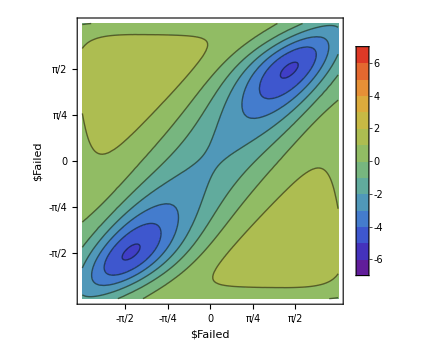
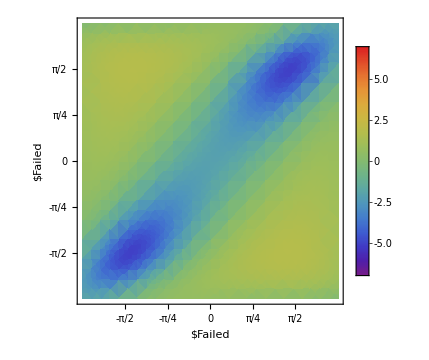
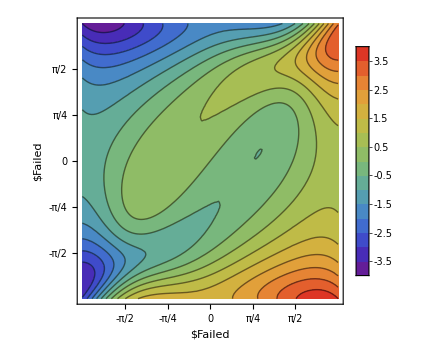
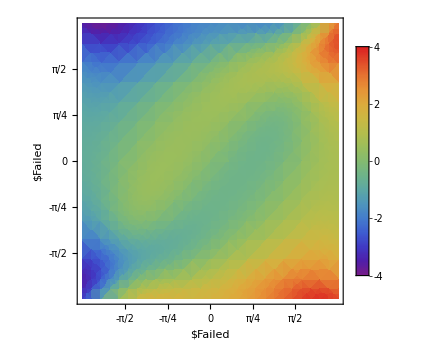
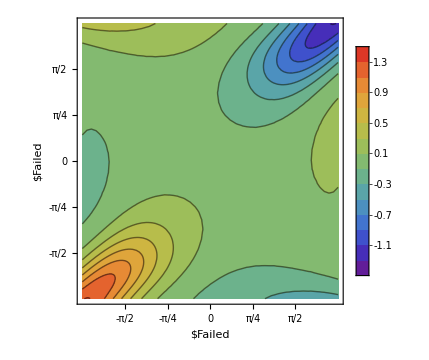
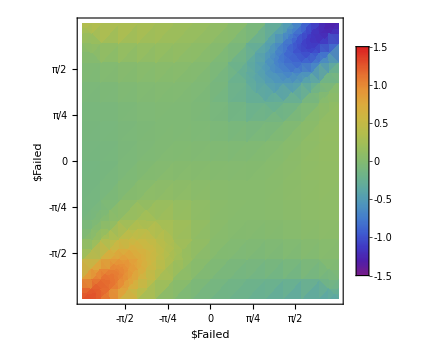
-Graphics- | -Graphics- | local maximum 1.825
local minimum -5.13241
-Graphics- | -Graphics- | local maximum 0.501791
local minimum -0.501791
-Graphics- | -Graphics- | local maximum 1.46143
local minimum -1.46143

```mathematica
localCurvaturePicture[7, 6, 5]
```

Need to be reminded of what the swimmer looks like? Here’s a function that juxtaposes a density plot of the component of curvature corresponding to longitudinal translation — the component of curvature we care about most — with a picture of the swimmer.

```mathematica
drawRobot[aTail_, aBody_, aHead_] := Show[{water, body, headPivotDot, head, tailPivotDot, tail} /. equalGaps /. {aT -> aTail, aB -> aBody, aH -> aHead} /.{x[t] -> 0, y[t] -> 0, θ[t] -> 0, η[t] -> 0, τ[t] -> 0}, PlotRange -> {{-30, 30}, {-10, 10}}, ImageSize -> Medium]
```

```mathematica
ΩxPlusRobot[aTail_, aBody_, aHead_]:= Grid[{{ΩxDensityPlot[aTail, aBody, aHead], drawRobot[aTail, aBody, aHead]}}]
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

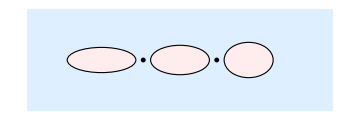
-Graphics- | -Graphics-

```mathematica
ΩxPlusRobot[7, 6, 5]
```

Okay, let’s move on to some simulations. The idea is to actuate the head joint periodically and allow the tail joint to oscillate freely, but we’d like the tail joint to be critically (or maybe slightly over-) damped. Here’s the damping constant that will make the tail joint critically damped, along with that joint’s undamped natural frequency.

```mathematica
criticalC = 2 √((mRotT + mLatT (aT + gapTB)^2) k);
naturalFrequency = √(k/(mRotT + mLatT (aT + gapTB)^2));
```

```mathematica
fiberwiseODE = {SE2VelocityInBodyFrame[[1]] == - cheatA[[1]], SE2VelocityInBodyFrame[[2]] == - cheatA[[2]], SE2VelocityInBodyFrame[[3]] == - cheatA[[3]]};
```

```mathematica
tailHingeODE = D[D[L, τ'[t]], t] - D[L, τ[t]] == - c τ'[t];
```

```mathematica
se2matrix[{{x_, y_, θ_}}] := {{Cos[θ], - Sin[θ], x}, {Sin[θ], Cos[θ], y}, {0, 0, 1}};
```

```mathematica
pathPlots[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_] := Module[{freq},
freq = frequency /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} ;
shapeChange = {η[t] -> amplitude Cos[freq t]};
duration = (100 π)/freq;
solution = NDSolve[{{fiberwiseODE, tailHingeODE} /. c -> dampingConstant /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead}  /. shapeChange /. D[shapeChange, t], x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, τ'[0] == 0}, {x[t], y[t], θ[t], x'[t], y'[t], θ'[t], τ[t], τ'[t]}, {t, 0, duration},Method->{"EquationSimplification"->"Residual"}];
firstCycle = Inverse[se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> 0]].se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> (2 π)/freq ] // {#[[1, 3]], #[[2, 3]], ArcCos[#[[1, 1]]]}&;
eventualCyclePhase = Inverse[se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> duration - (2 π)/freq]].se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> duration] // {#[[1, 3]], #[[2, 3]], ArcCos[#[[1, 1]]]}&;
shapePathPlot = ParametricPlot[{η[t] /. shapeChange, First[τ[t] /. solution]}, {t, duration - (8 π)/freq, duration}, PlotRange -> All, PlotStyle -> Black]/.Line[x_]:>{Arrowheads[.05],Arrow[x]};
Grid[{{Show[{ΩxDensityPlot[aForTail, aForBody, aForHead], shapePathPlot}], Show[{ΩyDensityPlot[aForTail, aForBody, aForHead], shapePathPlot}], Show[{ΩθDensityPlot[aForTail, aForBody, aForHead], shapePathPlot}]},
{"displacement after first cycle =", "final cycle phase = "}, {firstCycle, eventualCyclePhase}}]
];
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

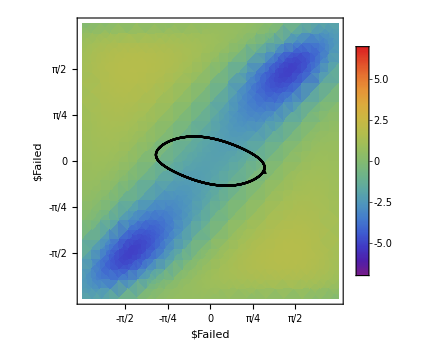
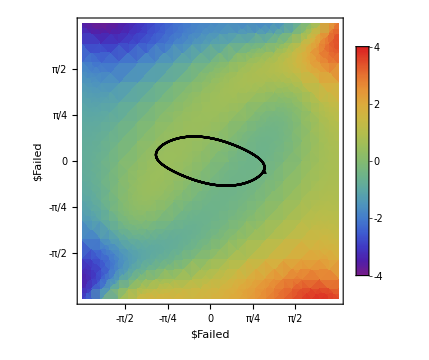
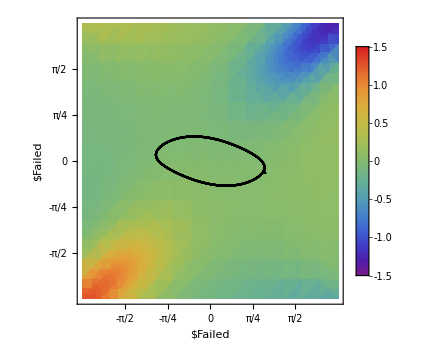
-Graphics- | -Graphics- | -Graphics-
displacement after first cycle = | final cycle phase =  | 
{1.671,0.605449,0.0601544} | {1.86214,0.394299,3.94248×10^-8} |

```mathematica
pathPlots[1, 10 naturalFrequency, 1, criticalC,7, 6, 5]
```

```mathematica
phaseInSteadyState[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_]:= Module[{freq},
freq = frequency /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} ;
shapeChange = {η[t] -> amplitude Cos[freq t]};
duration = (100 π)/freq;
solution = NDSolve[{{fiberwiseODE, tailHingeODE} /. c -> dampingConstant /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead}  /. shapeChange /. D[shapeChange, t], x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, τ'[0] == 0}, {x[t], y[t], θ[t], x'[t], y'[t], θ'[t], τ[t], τ'[t]}, {t, 0, duration},Method->{"EquationSimplification"->"Residual"}];
eventualCyclePhase = Inverse[se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> duration - (2 π)/freq]].se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> duration] // {#[[1, 3]], #[[2, 3]], ArcCos[#[[1, 1]]]}&
];
```

```mathematica
phaseInSteadyState[1, 10 naturalFrequency, 1, criticalC,7, 6, 5]
```

{1.86214,0.394299,3.94248×10^-8}

```mathematica
fullPathPlots[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_] := Module[{freq},
freq = frequency /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} ;
shapeChange = {η[t] -> amplitude Cos[freq t]};
duration = (100 π)/freq;
solution = NDSolve[{{fiberwiseODE, tailHingeODE} /. c -> dampingConstant /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead}  /. shapeChange /. D[shapeChange, t], x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, τ'[0] == 0}, {x[t], y[t], θ[t], x'[t], y'[t], θ'[t], τ[t], τ'[t]}, {t, 0, duration},Method->{"EquationSimplification"->"Residual"}];
firstCycle = Inverse[se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> 0]].se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> (2 π)/freq ] // {#[[1, 3]], #[[2, 3]], ArcCos[#[[1, 1]]]}&;
eventualCyclePhase = Inverse[se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> duration - (2 π)/freq]].se2matrix[{x[t], y[t], θ[t]} /. solution /. t -> duration] // {#[[1, 3]], #[[2, 3]], ArcCos[#[[1, 1]]]}&;
shapePathPlot = ParametricPlot[{η[t] /. shapeChange, First[τ[t] /. solution]}, {t, 0, duration}, PlotRange -> All, PlotStyle -> Black]/.Line[x_]:>{Arrowheads[.05],Arrow[x]};
Grid[{{Show[{ΩxDensityPlot[aForTail, aForBody, aForHead], shapePathPlot}], Show[{ΩyDensityPlot[aForTail, aForBody, aForHead], shapePathPlot}], Show[{ΩθDensityPlot[aForTail, aForBody, aForHead], shapePathPlot}]},
{"displacement after first cycle =", "final cycle phase = "}, {firstCycle, eventualCyclePhase}}]];
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

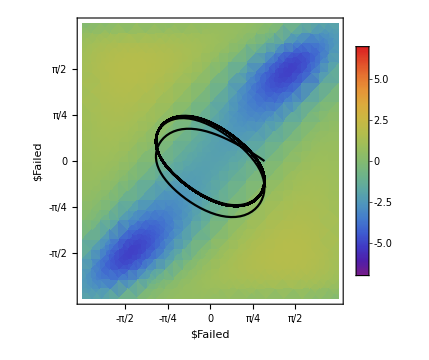
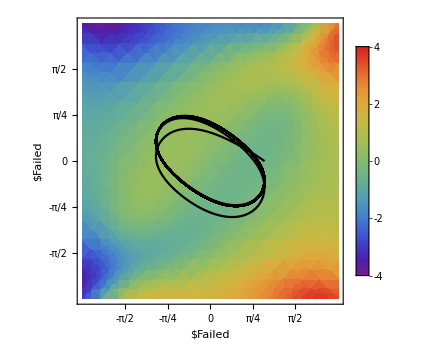
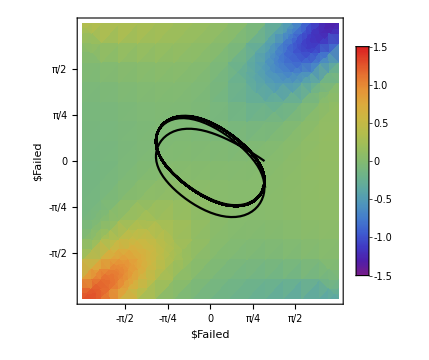
-Graphics- | -Graphics- | -Graphics-
displacement after first cycle = | final cycle phase =  | 
{2.19486,1.39334,0.198982} | {2.67563,0.833872,9.79404×10^-7} |

```mathematica
fullPathPlots[1, 5 naturalFrequency, 1, .2 criticalC,7, 6, 5]
```

These are also interesting plots to generate:

```mathematica
timePlots[amplitude_,frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_] := Module[{freq},
freq = frequency /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} ;
shapeChange = {η[t] -> amplitude Cos[freq t]};
duration = (100 π)/freq;
solution = NDSolve[{{fiberwiseODE, tailHingeODE} /. c -> dampingConstant /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead}  /. shapeChange /. D[shapeChange, t], x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, τ'[0] == 0}, {x[t], y[t], θ[t], x'[t], y'[t], θ'[t], τ[t], τ'[t]}, {t, 0, duration},Method->{"EquationSimplification"->"Residual"}];
trajectoryPlots = Plot[Evaluate[{x[t], y[t], θ[t]} /. solution], {t, 0, duration}, AxesLabel -> matex18/@{t, "\\text{fiber variables}"},PlotLegends -> matex18/@{x[t], y[t], θ[t]}, ImageSize -> Medium];
jointAnglePlots = Plot[Evaluate[{η[t], τ[t]} /. solution /. shapeChange], {t, 0, duration}, AxesLabel -> matex18/@{"t", "\\text{joint angle}"}, PlotLegends -> matex18/@{η[t], τ[t]}, ImageSize -> Medium];
Grid[{{trajectoryPlots, jointAnglePlots}}]];
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

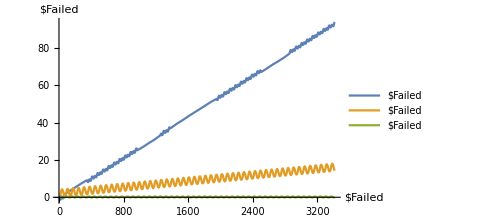
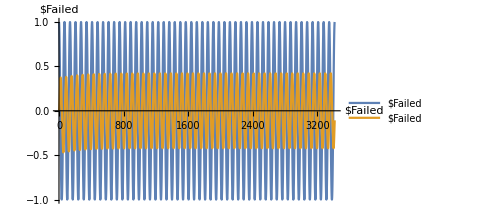
-Graphics- | -Graphics-

```mathematica
timePlots[1, 10 naturalFrequency, 1,criticalC,7, 6, 5]
```

```mathematica
momentumCheck[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_] := Module[{freq},
freq = frequency /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} ;
shapeChange = {η[t] -> amplitude Cos[freq t]};
duration = (100 π)/freq;
solution = NDSolve[{{fiberwiseODE, tailHingeODE} /. c -> dampingConstant /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead}  /. shapeChange /. D[shapeChange, t], x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, τ'[0] == 0}, {x[t], y[t], θ[t], x'[t], y'[t], θ'[t], τ[t], τ'[t]}, {t, 0, duration},Method->{"EquationSimplification"->"Residual"}];
Plot[Evaluate[{J1, J2, J3} /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} /. shapeChange /. D[shapeChange, t] /. solution ], {t, 0, duration}, PlotRange -> All, AxesLabel -> matex18/@{"t", "\\text{momentum}"}, PlotLegends-> matex18/@{"J1", "J2", "J3"}]];
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

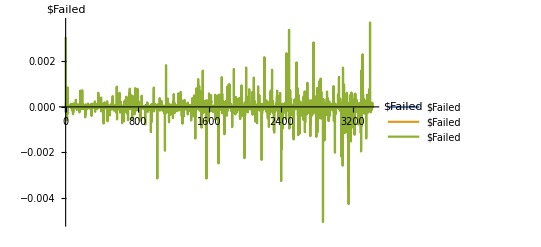

```mathematica
momentumCheck[1, 10 naturalFrequency, 1, criticalC, 7, 6, 5]
```

Plots are all well and good, but let’s make a movie!

```mathematica
movie[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_] := Module[{freq},
freq = frequency /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} ;
shapeChange = {η[t] -> amplitude Cos[freq t]} ;
duration = (100 π)/freq;
solution = NDSolve[{{fiberwiseODE, tailHingeODE} /. c -> dampingConstant /. ellipses /. k -> springConstant  /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead}  /. shapeChange /. D[shapeChange, t], x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, τ'[0] == 0}, {x[t], y[t], θ[t], x'[t], y'[t], θ'[t], τ[t], τ'[t]}, {t, 0, duration},Method->{"EquationSimplification"->"Residual"}];
movieFrame[time_] := Show[{water, body, headPivotDot, head, tailPivotDot, tail} /. equalGaps /. {aT -> aForTail, aB -> aForBody, aH -> aForHead} /. shapeChange /. solution /. t ->  time, PlotRange -> {{-50, 150}, {-100, 100}}];
numberOfFrames = 300;
movieFrames = Table[movieFrame[k], {k, 0, 60/100 duration,duration/numberOfFrames}];
ListAnimate[movieFrames]
];
```

```mathematica
movie[1, 5 naturalFrequency, 1, criticalC,10, 10, 10]
```

Okay, to recap ... Here are the commands I've defined to explore the behavior of this system:

drawRobot[aTail_, aBody_, aHead_]

cartoon[aTail_, aBody_, aHead_]

ΩxContourPlot[aTail_, aBody_, aHead_]
ΩxDensityPlot[aTail_, aBody_, aHead_]

ΩyContourPlot[aTail_, aBody_, aHead_]
ΩxDensityPlot[aTail_, aBody_, aHead_]

ΩθContourPlot[aTail_, aBody_, aHead_]
ΩθDensityPlot[aTail_, aBody_, aHead_]

pathPlots[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_]
fullPathPlots[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_]

timePlots[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_]

momentumCheck[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_]

movie[amplitude_, frequency_, springConstant_, dampingConstant_, aForTail_, aForBody_, aForHead_]

Since the natural frequency of the tail joint varies with the spring constant and we’re able to specify the forcing frequency in terms of the natural frequency, we may as well fix the spring constant and vary only the forcing frequency. I propose that we also fix the damping constant to ensure critical damping, leading to the following functions with pared-down arguments...

#### This is where functions Joe might want to call are defined.

Each of the following functions takes five arguments, in this order:

  1. The amplitude of head oscillation, in radians. This should be between 0 and 1.
  2. The frequency of head oscillation, as a multiple of the tail joint’s undamped natural frequency. This should be between 0.5 and 20.
  3, 4, 5. Parameters determining the eccentricity of the tail, body, and head ellipses, in that order. These should each be between 5 (for a fat ellipse) and 10 (for a skinny ellipse). 
  
The ranges I’ve proposed for these parameters are arbitrary; I just think they’re probably conservative enough to prevent the system’s dynamics from leading to overlaps between ellipses. Feel free to experiment with values outside these ranges.

```mathematica
steadyStateDisplacementPerCycleForJoe[headAmp_, headSpeed_, tailFatness_, bodyFatness_, headFatness_]:= phaseInSteadyState[headAmp, headSpeed naturalFrequency, 1, criticalC,tailFatness, bodyFatness, headFatness];
```

```mathematica
curvaturePlotsForJoe[headAmp_, headSpeed_, tailFatness_, bodyFatness_, headFatness_]:= pathPlots[headAmp, headSpeed naturalFrequency, 1, criticalC, tailFatness, bodyFatness, headFatness]
```

```mathematica
movieForJoe[headAmp_, headSpeed_, tailFatness_, bodyFatness_, headFatness_]:= movie[headAmp, headSpeed naturalFrequency, 1, criticalC, tailFatness, bodyFatness, headFatness]
```

#### Here's an example of their use.

```mathematica
steadyStateDisplacementPerCycleForJoe[1, 10, 8, 8, 6]
```

{5.62076,1.12264,2.38419×10^-7}

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

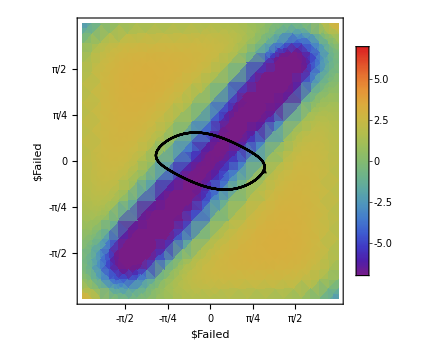
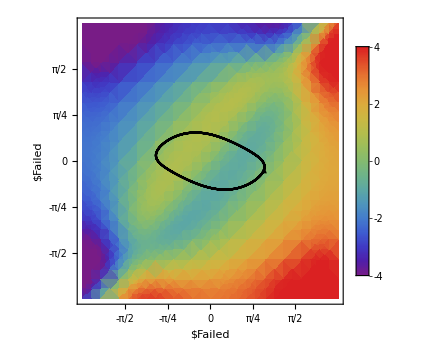
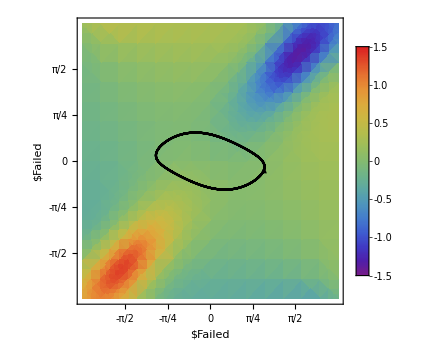
-Graphics- | -Graphics- | -Graphics-
displacement after first cycle = | final cycle phase =  | 
{5.2645,1.088,0.0783112} | {5.62076,1.12264,2.38419×10^-7} |

```mathematica
curvaturePlotsForJoe[1, 10, 8, 8, 6]
```

```mathematica
movieForJoe[1, 10, 8, 8, 6]
```

#### Here are two commands for Jack.

Any integer between 5 and 10 would be a reasonable argument for these commands.

```mathematica
howPointyIsIt[choiceOfSemimajorAxis_]:= drawRobot[choiceOfSemimajorAxis, choiceOfSemimajorAxis, choiceOfSemimajorAxis]
```

```mathematica
showMeA[choiceOfSemimajorAxis_]:= {{Axη, Axτ}, {Ayη, Ayτ}, {Aθη, Aθτ}}/. ellipses /. equalGaps /. {aH -> choiceOfSemimajorAxis, aB -> choiceOfSemimajorAxis, aT -> choiceOfSemimajorAxis} // FullSimplify
```

#### Here’s an example of their use.

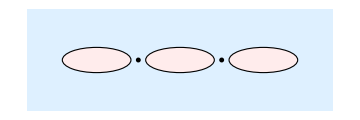

```mathematica
howPointyIsIt[7]
```

```mathematica
showMeA[7]
```

{{-((17 (1902938906458884 Sin[η[t]]+67008778932370 Sin[2 η[t]]+430635669371306 Sin[η[t]-2 τ[t]]+1493437037304534 Sin[η[t]-τ[t]]-1027399540055203 Sin[τ[t]]-430803566835808 Sin[2 τ[t]]+497812345768178 Sin[η[t]+τ[t]]+13072332995 (2077 Sin[2 (η[t]+τ[t])]+2401 Sin[2 η[t]+τ[t]])+81648799884050 Sin[η[t]+2 τ[t]]))/(6950344987924878+4433052168153896 Cos[τ[t]]+272004488 Cos[η[t]] (16297717+4667544 Cos[τ[t]]-2295085 Cos[2 τ[t]])+58516346103350 Cos[2 τ[t]]-20770 Cos[2 η[t]] (-2817349355+30056495924 Cos[τ[t]]+17187045685 Cos[2 τ[t]])-829341683912 Sin[η[t]] (4802 Sin[τ[t]]+2077 Sin[2 τ[t]])-4154 Sin[2 η[t]] (414670841956 Sin[τ[t]]+158422965851 Sin[2 τ[t]]))),(17 (2401 (-427904848003-414670841956 Cos[τ[t]]+13072332995 Cos[2 τ[t]]) Sin[η[t]]+(-430803566835808-348986869487256 Cos[τ[t]]+27151235630615 Cos[2 τ[t]]) Sin[2 η[t]]+9604 (198140244321+207335420978 Cos[η[t]]+53340740239 Cos[2 η[t]]) Sin[τ[t]]+13072332995 (5126+2401 Cos[η[t]]+2077 Cos[2 η[t]]) Sin[2 τ[t]]))/(6950344987924878+4433052168153896 Cos[τ[t]]+272004488 Cos[η[t]] (16297717+4667544 Cos[τ[t]]-2295085 Cos[2 τ[t]])+58516346103350 Cos[2 τ[t]]-20770 Cos[2 η[t]] (-2817349355+30056495924 Cos[τ[t]]+17187045685 Cos[2 τ[t]])-829341683912 Sin[η[t]] (4802 Sin[τ[t]]+2077 Sin[2 τ[t]])-4154 Sin[2 η[t]] (414670841956 Sin[τ[t]]+158422965851 Sin[2 τ[t]]))},{(17 (306147010883749 Cos[τ[t]]+13072332995 Cos[2 η[t]] (3049+2401 Cos[τ[t]])+118841571190429 Cos[2 τ[t]]+4802 Cos[η[t]] (166502931985+198291271752 Cos[τ[t]]+40174617743 Cos[2 τ[t]])-2401 (-66097090584+13072332995 Sin[2 η[t]] Sin[τ[t]]-34006164050 Sin[η[t]] Sin[2 τ[t]])))/(6950344987924878+4433052168153896 Cos[τ[t]]+272004488 Cos[η[t]] (16297717+4667544 Cos[τ[t]]-2295085 Cos[2 τ[t]])+58516346103350 Cos[2 τ[t]]-20770 Cos[2 η[t]] (-2817349355+30056495924 Cos[τ[t]]+17187045685 Cos[2 τ[t]])-829341683912 Sin[η[t]] (4802 Sin[τ[t]]+2077 Sin[2 τ[t]])-4154 Sin[2 η[t]] (414670841956 Sin[τ[t]]+158422965851 Sin[2 τ[t]])),(17 (158699114492184+306147010883749 Cos[η[t]]+118841571190429 Cos[2 η[t]]+4802 (166502931985+198291271752 Cos[η[t]]+40174617743 Cos[2 η[t]]) Cos[τ[t]]+13072332995 (3049+2401 Cos[η[t]]) Cos[2 τ[t]]+81648799884050 Sin[2 η[t]] Sin[τ[t]]-31386671520995 Sin[η[t]] Sin[2 τ[t]]))/(6950344987924878+4433052168153896 Cos[τ[t]]+272004488 Cos[η[t]] (16297717+4667544 Cos[τ[t]]-2295085 Cos[2 τ[t]])+58516346103350 Cos[2 τ[t]]-20770 Cos[2 η[t]] (-2817349355+30056495924 Cos[τ[t]]+17187045685 Cos[2 τ[t]])-829341683912 Sin[η[t]] (4802 Sin[τ[t]]+2077 Sin[2 τ[t]])-4154 Sin[2 η[t]] (414670841956 Sin[τ[t]]+158422965851 Sin[2 τ[t]]))},{(952862342614013+1108263042038474 Cos[η[t]]+27151235630615 Cos[2 η[t]]-293352012228338 Cos[η[t]-2 τ[t]]-339113231275994 Cos[η[t]-τ[t]]-311961995645379 Cos[2 τ[t]]+656511460260362 Cos[η[t]+τ[t]]+27151235630615 Cos[2 (η[t]+τ[t])]+137283657142968 Cos[η[t]+2 τ[t]])/(3475172493962439+2216526084076948 Cos[τ[t]]+136002244 Cos[η[t]] (16297717+4667544 Cos[τ[t]]-2295085 Cos[2 τ[t]])+29258173051675 Cos[2 τ[t]]-10385 Cos[2 η[t]] (-2817349355+30056495924 Cos[τ[t]]+17187045685 Cos[2 τ[t]])-414670841956 Sin[η[t]] (4802 Sin[τ[t]]+2077 Sin[2 τ[t]])-2077 Sin[2 η[t]] (414670841956 Sin[τ[t]]+158422965851 Sin[2 τ[t]])),(952862342614013-311961995645379 Cos[2 η[t]]+68001122 (16297717+4667544 Cos[η[t]]-2295085 Cos[2 η[t]]) Cos[τ[t]]+54302471261230 Cos[η[t]]^2 Cos[2 τ[t]]-207335420978 (4802 Sin[η[t]]+2077 Sin[2 η[t]]) Sin[τ[t]]-27151235630615 Sin[2 η[t]] Sin[2 τ[t]])/(-3475172493962439-29258173051675 Cos[2 η[t]]+136002244 (-16297717+2295085 Cos[2 η[t]]) Cos[τ[t]]+51925 (-563469871+3437409137 Cos[2 η[t]]) Cos[2 τ[t]]+136002244 Cos[η[t]] (-16297717-4667544 Cos[τ[t]]+2295085 Cos[2 τ[t]])+414670841956 (4802 Sin[η[t]]+2077 Sin[2 η[t]]) Sin[τ[t]]+2077 (414670841956 Sin[η[t]]+158422965851 Sin[2 η[t]]) Sin[2 τ[t]])}}

```mathematica
showMeA[7] /. joint_[t] -> joint // MatrixForm
```

(-(17 (1902938906458884 Sin[η]+67008778932370 Sin[2 η]+430635669371306 Sin[η-2 τ]+1493437037304534 Sin[η-τ]-1027399540055203 Sin[τ]-430803566835808 Sin[2 τ]+497812345768178 Sin[η+τ]+13072332995 (2077 Sin[2 (η+τ)]+2401 Sin[2 η+τ])+81648799884050 Sin[η+2 τ]))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ])) | (17 (2401 (-427904848003-414670841956 Cos[τ]+13072332995 Cos[2 τ]) Sin[η]+(-430803566835808-348986869487256 Cos[τ]+27151235630615 Cos[2 τ]) Sin[2 η]+9604 (198140244321+207335420978 Cos[η]+53340740239 Cos[2 η]) Sin[τ]+13072332995 (5126+2401 Cos[η]+2077 Cos[2 η]) Sin[2 τ]))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ]))
(17 (306147010883749 Cos[τ]+13072332995 Cos[2 η] (3049+2401 Cos[τ])+118841571190429 Cos[2 τ]+4802 Cos[η] (166502931985+198291271752 Cos[τ]+40174617743 Cos[2 τ])-2401 (-66097090584+13072332995 Sin[2 η] Sin[τ]-34006164050 Sin[η] Sin[2 τ])))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ])) | (17 (158699114492184+306147010883749 Cos[η]+118841571190429 Cos[2 η]+4802 (166502931985+198291271752 Cos[η]+40174617743 Cos[2 η]) Cos[τ]+13072332995 (3049+2401 Cos[η]) Cos[2 τ]+81648799884050 Sin[2 η] Sin[τ]-31386671520995 Sin[η] Sin[2 τ]))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ]))
(952862342614013+1108263042038474 Cos[η]+27151235630615 Cos[2 η]-293352012228338 Cos[η-2 τ]-339113231275994 Cos[η-τ]-311961995645379 Cos[2 τ]+656511460260362 Cos[η+τ]+27151235630615 Cos[2 (η+τ)]+137283657142968 Cos[η+2 τ])/(3475172493962439+2216526084076948 Cos[τ]+136002244 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+29258173051675 Cos[2 τ]-10385 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-414670841956 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-2077 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ])) | (952862342614013-311961995645379 Cos[2 η]+68001122 (16297717+4667544 Cos[η]-2295085 Cos[2 η]) Cos[τ]+54302471261230 Cos[η]^2 Cos[2 τ]-207335420978 (4802 Sin[η]+2077 Sin[2 η]) Sin[τ]-27151235630615 Sin[2 η] Sin[2 τ])/(-3475172493962439-29258173051675 Cos[2 η]+136002244 (-16297717+2295085 Cos[2 η]) Cos[τ]+51925 (-563469871+3437409137 Cos[2 η]) Cos[2 τ]+136002244 Cos[η] (-16297717-4667544 Cos[τ]+2295085 Cos[2 τ])+414670841956 (4802 Sin[η]+2077 Sin[2 η]) Sin[τ]+2077 (414670841956 Sin[η]+158422965851 Sin[2 η]) Sin[2 τ]))

```mathematica
jackTailODE[choiceOfSemimajorAxis_]:= tailHingeODE /. ellipses  /. equalGaps /. {aH -> choiceOfSemimajorAxis, aB -> choiceOfSemimajorAxis, aT -> choiceOfSemimajorAxis} // FullSimplify
```

```mathematica
jackTailODE[7]
```

k τ[t]+c τ'[t]+1/392 π (-8308 (-Sin[2 (θ[t]-τ[t])] x'[t]^2+2 Cos[2 (θ[t]-τ[t])] x'[t] y'[t]+Sin[2 (θ[t]-τ[t])] y'[t]^2)+141236 (Cos[θ[t]-2 τ[t]] x'[t]+Sin[θ[t]-2 τ[t]] y'[t]) θ'[t]+289 (4802 Sin[τ[t]]+2077 Sin[2 τ[t]]) θ'[t]^2+163268 Cos[θ[t]-τ[t]] y''[t])==833/2 π Sin[θ[t]-τ[t]] x''[t]+14161/4 π Cos[τ[t]] θ''[t]+(72315051 π (θ''[t]-τ''[t]))/19208

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[k τ[t]+c τ'[t]+1/392 π (-8308 (-Sin[2 (θ[t]-τ[t])] x'[t]^2+2 Cos[2 (θ[t]-τ[t])] x'[t] y'[t]+Sin[2 (θ[t]-τ[t])] y'[t]^2)+141236 (Cos[θ[t]-2 τ[t]] x'[t]+Sin[θ[t]-2 τ[t]] y'[t]) θ'[t]+289 (4802 Sin[τ[t]]+2077 Sin[2 τ[t]]) θ'[t]^2+163268 Cos[θ[t]-τ[t]] y''[t])==833/2 π Sin[θ[t]-τ[t]] x''[t]+14161/4 π Cos[τ[t]] θ''[t]+(72315051 π (θ''[t]-τ''[t]))/19208,{x[t],y[t],θ[t],τ[t],x[t],y[t],θ[t],τ[t]},{t}]

```mathematica
%392 // InputForm
```

k*τ[t] + c*Derivative[1][τ][t] + (Pi*(-8308*(-(Sin[2*(θ[t] - τ[t])]*Derivative[1][x][t]^2) + 2*Cos[2*(θ[t] - τ[t])]*Derivative[1][x][t]*Derivative[1][y][t] + 
       Sin[2*(θ[t] - τ[t])]*Derivative[1][y][t]^2) + 141236*(Cos[θ[t] - 2*τ[t]]*Derivative[1][x][t] + Sin[θ[t] - 2*τ[t]]*Derivative[1][y][t])*Derivative[1][θ][t] + 
     289*(4802*Sin[τ[t]] + 2077*Sin[2*τ[t]])*Derivative[1][θ][t]^2 + 163268*Cos[θ[t] - τ[t]]*Derivative[2][y][t]))/392 == 
 (833*Pi*Sin[θ[t] - τ[t]]*Derivative[2][x][t])/2 + (14161*Pi*Cos[τ[t]]*Derivative[2][θ][t])/4 + (72315051*Pi*(Derivative[2][θ][t] - Derivative[2][τ][t]))/19208

```mathematica
showMeA[7] /. joint_[t] -> joint
```

{{-((17 (1902938906458884 Sin[η]+67008778932370 Sin[2 η]+430635669371306 Sin[η-2 τ]+1493437037304534 Sin[η-τ]-1027399540055203 Sin[τ]-430803566835808 Sin[2 τ]+497812345768178 Sin[η+τ]+13072332995 (2077 Sin[2 (η+τ)]+2401 Sin[2 η+τ])+81648799884050 Sin[η+2 τ]))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ]))),(17 (2401 (-427904848003-414670841956 Cos[τ]+13072332995 Cos[2 τ]) Sin[η]+(-430803566835808-348986869487256 Cos[τ]+27151235630615 Cos[2 τ]) Sin[2 η]+9604 (198140244321+207335420978 Cos[η]+53340740239 Cos[2 η]) Sin[τ]+13072332995 (5126+2401 Cos[η]+2077 Cos[2 η]) Sin[2 τ]))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ]))},{(17 (306147010883749 Cos[τ]+13072332995 Cos[2 η] (3049+2401 Cos[τ])+118841571190429 Cos[2 τ]+4802 Cos[η] (166502931985+198291271752 Cos[τ]+40174617743 Cos[2 τ])-2401 (-66097090584+13072332995 Sin[2 η] Sin[τ]-34006164050 Sin[η] Sin[2 τ])))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ])),(17 (158699114492184+306147010883749 Cos[η]+118841571190429 Cos[2 η]+4802 (166502931985+198291271752 Cos[η]+40174617743 Cos[2 η]) Cos[τ]+13072332995 (3049+2401 Cos[η]) Cos[2 τ]+81648799884050 Sin[2 η] Sin[τ]-31386671520995 Sin[η] Sin[2 τ]))/(6950344987924878+4433052168153896 Cos[τ]+272004488 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+58516346103350 Cos[2 τ]-20770 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-829341683912 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-4154 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ]))},{(952862342614013+1108263042038474 Cos[η]+27151235630615 Cos[2 η]-293352012228338 Cos[η-2 τ]-339113231275994 Cos[η-τ]-311961995645379 Cos[2 τ]+656511460260362 Cos[η+τ]+27151235630615 Cos[2 (η+τ)]+137283657142968 Cos[η+2 τ])/(3475172493962439+2216526084076948 Cos[τ]+136002244 Cos[η] (16297717+4667544 Cos[τ]-2295085 Cos[2 τ])+29258173051675 Cos[2 τ]-10385 Cos[2 η] (-2817349355+30056495924 Cos[τ]+17187045685 Cos[2 τ])-414670841956 Sin[η] (4802 Sin[τ]+2077 Sin[2 τ])-2077 Sin[2 η] (414670841956 Sin[τ]+158422965851 Sin[2 τ])),(952862342614013-311961995645379 Cos[2 η]+68001122 (16297717+4667544 Cos[η]-2295085 Cos[2 η]) Cos[τ]+54302471261230 Cos[η]^2 Cos[2 τ]-207335420978 (4802 Sin[η]+2077 Sin[2 η]) Sin[τ]-27151235630615 Sin[2 η] Sin[2 τ])/(-3475172493962439-29258173051675 Cos[2 η]+136002244 (-16297717+2295085 Cos[2 η]) Cos[τ]+51925 (-563469871+3437409137 Cos[2 η]) Cos[2 τ]+136002244 Cos[η] (-16297717-4667544 Cos[τ]+2295085 Cos[2 τ])+414670841956 (4802 Sin[η]+2077 Sin[2 η]) Sin[τ]+2077 (414670841956 Sin[η]+158422965851 Sin[2 η]) Sin[2 τ])}}

```mathematica
%144 // InputForm
```

{{(-17*(1902938906458884*Sin[η] + 67008778932370*Sin[2*η] + 430635669371306*Sin[η - 2*τ] + 1493437037304534*Sin[η - τ] - 1027399540055203*Sin[τ] - 430803566835808*Sin[2*τ] + 
     497812345768178*Sin[η + τ] + 13072332995*(2077*Sin[2*(η + τ)] + 2401*Sin[2*η + τ]) + 81648799884050*Sin[η + 2*τ]))/
   (6950344987924878 + 4433052168153896*Cos[τ] + 272004488*Cos[η]*(16297717 + 4667544*Cos[τ] - 2295085*Cos[2*τ]) + 58516346103350*Cos[2*τ] - 
    20770*Cos[2*η]*(-2817349355 + 30056495924*Cos[τ] + 17187045685*Cos[2*τ]) - 829341683912*Sin[η]*(4802*Sin[τ] + 2077*Sin[2*τ]) - 
    4154*Sin[2*η]*(414670841956*Sin[τ] + 158422965851*Sin[2*τ])), 
  (17*(2401*(-427904848003 - 414670841956*Cos[τ] + 13072332995*Cos[2*τ])*Sin[η] + (-430803566835808 - 348986869487256*Cos[τ] + 27151235630615*Cos[2*τ])*Sin[2*η] + 
     9604*(198140244321 + 207335420978*Cos[η] + 53340740239*Cos[2*η])*Sin[τ] + 13072332995*(5126 + 2401*Cos[η] + 2077*Cos[2*η])*Sin[2*τ]))/
   (6950344987924878 + 4433052168153896*Cos[τ] + 272004488*Cos[η]*(16297717 + 4667544*Cos[τ] - 2295085*Cos[2*τ]) + 58516346103350*Cos[2*τ] - 
    20770*Cos[2*η]*(-2817349355 + 30056495924*Cos[τ] + 17187045685*Cos[2*τ]) - 829341683912*Sin[η]*(4802*Sin[τ] + 2077*Sin[2*τ]) - 
    4154*Sin[2*η]*(414670841956*Sin[τ] + 158422965851*Sin[2*τ]))}, 
 {(17*(306147010883749*Cos[τ] + 13072332995*Cos[2*η]*(3049 + 2401*Cos[τ]) + 118841571190429*Cos[2*τ] + 4802*Cos[η]*(166502931985 + 198291271752*Cos[τ] + 40174617743*Cos[2*τ]) - 
     2401*(-66097090584 + 13072332995*Sin[2*η]*Sin[τ] - 34006164050*Sin[η]*Sin[2*τ])))/(6950344987924878 + 4433052168153896*Cos[τ] + 
    272004488*Cos[η]*(16297717 + 4667544*Cos[τ] - 2295085*Cos[2*τ]) + 58516346103350*Cos[2*τ] - 20770*Cos[2*η]*(-2817349355 + 30056495924*Cos[τ] + 17187045685*Cos[2*τ]) - 
    829341683912*Sin[η]*(4802*Sin[τ] + 2077*Sin[2*τ]) - 4154*Sin[2*η]*(414670841956*Sin[τ] + 158422965851*Sin[2*τ])), 
  (17*(158699114492184 + 306147010883749*Cos[η] + 118841571190429*Cos[2*η] + 4802*(166502931985 + 198291271752*Cos[η] + 40174617743*Cos[2*η])*Cos[τ] + 
     13072332995*(3049 + 2401*Cos[η])*Cos[2*τ] + 81648799884050*Sin[2*η]*Sin[τ] - 31386671520995*Sin[η]*Sin[2*τ]))/
   (6950344987924878 + 4433052168153896*Cos[τ] + 272004488*Cos[η]*(16297717 + 4667544*Cos[τ] - 2295085*Cos[2*τ]) + 58516346103350*Cos[2*τ] - 
    20770*Cos[2*η]*(-2817349355 + 30056495924*Cos[τ] + 17187045685*Cos[2*τ]) - 829341683912*Sin[η]*(4802*Sin[τ] + 2077*Sin[2*τ]) - 
    4154*Sin[2*η]*(414670841956*Sin[τ] + 158422965851*Sin[2*τ]))}, 
 {(952862342614013 + 1108263042038474*Cos[η] + 27151235630615*Cos[2*η] - 293352012228338*Cos[η - 2*τ] - 339113231275994*Cos[η - τ] - 311961995645379*Cos[2*τ] + 
    656511460260362*Cos[η + τ] + 27151235630615*Cos[2*(η + τ)] + 137283657142968*Cos[η + 2*τ])/(3475172493962439 + 2216526084076948*Cos[τ] + 
    136002244*Cos[η]*(16297717 + 4667544*Cos[τ] - 2295085*Cos[2*τ]) + 29258173051675*Cos[2*τ] - 10385*Cos[2*η]*(-2817349355 + 30056495924*Cos[τ] + 17187045685*Cos[2*τ]) - 
    414670841956*Sin[η]*(4802*Sin[τ] + 2077*Sin[2*τ]) - 2077*Sin[2*η]*(414670841956*Sin[τ] + 158422965851*Sin[2*τ])), 
  (952862342614013 - 311961995645379*Cos[2*η] + 68001122*(16297717 + 4667544*Cos[η] - 2295085*Cos[2*η])*Cos[τ] + 54302471261230*Cos[η]^2*Cos[2*τ] - 
    207335420978*(4802*Sin[η] + 2077*Sin[2*η])*Sin[τ] - 27151235630615*Sin[2*η]*Sin[2*τ])/(-3475172493962439 - 29258173051675*Cos[2*η] + 
    136002244*(-16297717 + 2295085*Cos[2*η])*Cos[τ] + 51925*(-563469871 + 3437409137*Cos[2*η])*Cos[2*τ] + 136002244*Cos[η]*(-16297717 - 4667544*Cos[τ] + 2295085*Cos[2*τ]) + 
    414670841956*(4802*Sin[η] + 2077*Sin[2*η])*Sin[τ] + 2077*(414670841956*Sin[η] + 158422965851*Sin[2*η])*Sin[2*τ])}}

```mathematica
%145 /. {η -> a1, τ -> a2}
```

{{-((17 (-1027399540055203 Sin[InterpolatingFunction[…]]-430803566835808 Sin[2 InterpolatingFunction[…]]-1493437037304534 Sin[InterpolatingFunction[…]-InterpolatingFunction[…]]-430635669371306 Sin[2 InterpolatingFunction[…]-InterpolatingFunction[…]]+1902938906458884 Sin[InterpolatingFunction[…]]+67008778932370 Sin[2 InterpolatingFunction[…]]+497812345768178 Sin[InterpolatingFunction[…]+InterpolatingFunction[…]]+81648799884050 Sin[2 InterpolatingFunction[…]+InterpolatingFunction[…]]+13072332995 (2077 Sin[2 (InterpolatingFunction[…]+InterpolatingFunction[…])]+2401 Sin[InterpolatingFunction[…]+2 InterpolatingFunction[…]])))/(6950344987924878+4433052168153896 Cos[InterpolatingFunction[…]]+58516346103350 Cos[2 InterpolatingFunction[…]]+272004488 (16297717+4667544 Cos[InterpolatingFunction[…]]-2295085 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]-20770 (-2817349355+30056495924 Cos[InterpolatingFunction[…]]+17187045685 Cos[2 InterpolatingFunction[…]]) Cos[2 InterpolatingFunction[…]]-829341683912 (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]-4154 (414670841956 Sin[InterpolatingFunction[…]]+158422965851 Sin[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]])),(17 (9604 (198140244321+207335420978 Cos[InterpolatingFunction[…]]+53340740239 Cos[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]+13072332995 (5126+2401 Cos[InterpolatingFunction[…]]+2077 Cos[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]]+2401 (-427904848003-414670841956 Cos[InterpolatingFunction[…]]+13072332995 Cos[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]+(-430803566835808-348986869487256 Cos[InterpolatingFunction[…]]+27151235630615 Cos[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]]))/(6950344987924878+4433052168153896 Cos[InterpolatingFunction[…]]+58516346103350 Cos[2 InterpolatingFunction[…]]+272004488 (16297717+4667544 Cos[InterpolatingFunction[…]]-2295085 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]-20770 (-2817349355+30056495924 Cos[InterpolatingFunction[…]]+17187045685 Cos[2 InterpolatingFunction[…]]) Cos[2 InterpolatingFunction[…]]-829341683912 (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]-4154 (414670841956 Sin[InterpolatingFunction[…]]+158422965851 Sin[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]])},{(17 (306147010883749 Cos[InterpolatingFunction[…]]+118841571190429 Cos[2 InterpolatingFunction[…]]+4802 (166502931985+198291271752 Cos[InterpolatingFunction[…]]+40174617743 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]+13072332995 (3049+2401 Cos[InterpolatingFunction[…]]) Cos[2 InterpolatingFunction[…]]-2401 (-66097090584-34006164050 Sin[2 InterpolatingFunction[…]] Sin[InterpolatingFunction[…]]+13072332995 Sin[InterpolatingFunction[…]] Sin[2 InterpolatingFunction[…]])))/(6950344987924878+4433052168153896 Cos[InterpolatingFunction[…]]+58516346103350 Cos[2 InterpolatingFunction[…]]+272004488 (16297717+4667544 Cos[InterpolatingFunction[…]]-2295085 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]-20770 (-2817349355+30056495924 Cos[InterpolatingFunction[…]]+17187045685 Cos[2 InterpolatingFunction[…]]) Cos[2 InterpolatingFunction[…]]-829341683912 (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]-4154 (414670841956 Sin[InterpolatingFunction[…]]+158422965851 Sin[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]]),(17 (158699114492184+306147010883749 Cos[InterpolatingFunction[…]]+13072332995 Cos[2 InterpolatingFunction[…]] (3049+2401 Cos[InterpolatingFunction[…]])+118841571190429 Cos[2 InterpolatingFunction[…]]+4802 Cos[InterpolatingFunction[…]] (166502931985+198291271752 Cos[InterpolatingFunction[…]]+40174617743 Cos[2 InterpolatingFunction[…]])-31386671520995 Sin[2 InterpolatingFunction[…]] Sin[InterpolatingFunction[…]]+81648799884050 Sin[InterpolatingFunction[…]] Sin[2 InterpolatingFunction[…]]))/(6950344987924878+4433052168153896 Cos[InterpolatingFunction[…]]+58516346103350 Cos[2 InterpolatingFunction[…]]+272004488 (16297717+4667544 Cos[InterpolatingFunction[…]]-2295085 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]-20770 (-2817349355+30056495924 Cos[InterpolatingFunction[…]]+17187045685 Cos[2 InterpolatingFunction[…]]) Cos[2 InterpolatingFunction[…]]-829341683912 (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]-4154 (414670841956 Sin[InterpolatingFunction[…]]+158422965851 Sin[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]])},{(952862342614013-311961995645379 Cos[2 InterpolatingFunction[…]]-339113231275994 Cos[InterpolatingFunction[…]-InterpolatingFunction[…]]-293352012228338 Cos[2 InterpolatingFunction[…]-InterpolatingFunction[…]]+1108263042038474 Cos[InterpolatingFunction[…]]+27151235630615 Cos[2 InterpolatingFunction[…]]+656511460260362 Cos[InterpolatingFunction[…]+InterpolatingFunction[…]]+27151235630615 Cos[2 (InterpolatingFunction[…]+InterpolatingFunction[…])]+137283657142968 Cos[2 InterpolatingFunction[…]+InterpolatingFunction[…]])/(3475172493962439+2216526084076948 Cos[InterpolatingFunction[…]]+29258173051675 Cos[2 InterpolatingFunction[…]]+136002244 (16297717+4667544 Cos[InterpolatingFunction[…]]-2295085 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]-10385 (-2817349355+30056495924 Cos[InterpolatingFunction[…]]+17187045685 Cos[2 InterpolatingFunction[…]]) Cos[2 InterpolatingFunction[…]]-414670841956 (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]]) Sin[InterpolatingFunction[…]]-2077 (414670841956 Sin[InterpolatingFunction[…]]+158422965851 Sin[2 InterpolatingFunction[…]]) Sin[2 InterpolatingFunction[…]]),(952862342614013+54302471261230 Cos[2 InterpolatingFunction[…]] Cos[InterpolatingFunction[…]]^2+68001122 Cos[InterpolatingFunction[…]] (16297717+4667544 Cos[InterpolatingFunction[…]]-2295085 Cos[2 InterpolatingFunction[…]])-311961995645379 Cos[2 InterpolatingFunction[…]]-27151235630615 Sin[2 InterpolatingFunction[…]] Sin[2 InterpolatingFunction[…]]-207335420978 Sin[InterpolatingFunction[…]] (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]]))/(-3475172493962439+136002244 (-16297717-4667544 Cos[InterpolatingFunction[…]]+2295085 Cos[2 InterpolatingFunction[…]]) Cos[InterpolatingFunction[…]]-29258173051675 Cos[2 InterpolatingFunction[…]]+136002244 Cos[InterpolatingFunction[…]] (-16297717+2295085 Cos[2 InterpolatingFunction[…]])+51925 Cos[2 InterpolatingFunction[…]] (-563469871+3437409137 Cos[2 InterpolatingFunction[…]])+414670841956 Sin[InterpolatingFunction[…]] (4802 Sin[InterpolatingFunction[…]]+2077 Sin[2 InterpolatingFunction[…]])+2077 Sin[2 InterpolatingFunction[…]] (414670841956 Sin[InterpolatingFunction[…]]+158422965851 Sin[2 InterpolatingFunction[…]]))}}

```mathematica
%274 /. {Sin[arg_] -> sin(arg), Cos[poop_] -> cos(poop)}
```

18 π

```mathematica
{1, 2, 3,4, 5} /. myInteger_Integer -> myInteger^2
```

{1,4,9,16,25}